{18666.7,47.619,9.52381,(2.79267×10^14 x^3)/((1+ⅇ^(√(1+x^2))) √(1+x^2))}

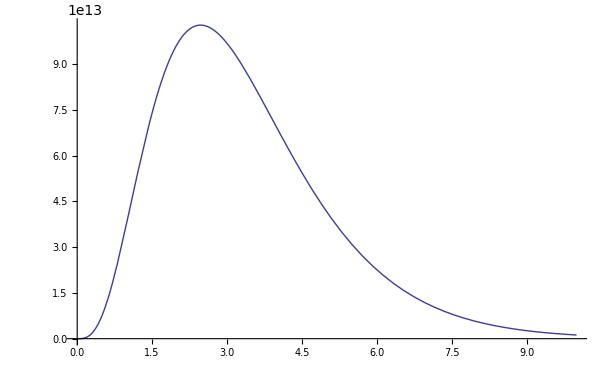

```mathematica
Module[
{
b=1,
m1=.105 10^9,
M1=2,
f,
xs,
xinv5
},
xs=1.96 10^12/m1;
xinv5=5 10^9/m1;
f[x_]:=M1 m1^2/(8π^2 Sqrt[x^2+1])x^3/(Exp[b Sqrt[x^2+1]]+1);
Print[{xs,xinv5,1 10^9/m1,f[x]}];
Plot[f[xinv],{xinv,0,10}]
]
```